```mathematica
ClearAll["Global`*"]
```

Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Needs["ComputerArithmetic`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

```mathematica
Get["funcs_for_stepMonitor_stringConv_plotSetOfInds_etc.m"]
(*Includes (as of 2018/03/29)
makeErrorData[x_,y_,yErr_]
kPlotStepMonitorData[kStepVals_]
gPlotStepMonitorData[gStepVals_]
tStringToSec[tString_]
minTidInd[tSearchString_,tStringArr_]
tPlotInds[inds_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tPlotRange[ind1_,ind2_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tablePlotMov[indStart_,indEnd1_,indEnd2_,mom_,momErr_,pRange_]
tablePlotsCombineAndAnimate[mov1_,mov2_]*)
```

Options

```mathematica
usePotForDensPot=False;(*For many orbits, the potential above FAST is not the total potential. For orbit 1612, there are ion beams throughout the observed period indicating the existence of a potential structure above FAST. (On the other hand for orbit 1607, for example, the potential above DOES appear to be the whole potential, because there are no observed ion beams.) *)
```

```mathematica
nTrials=100;
saveDataFiles=True;
```

### Load data

```mathematica
orbit=4682;
```

```mathematica
fName="20180813-orb_4862-densPA_36-MathematicaFINALQQ.csv";
```

```mathematica
inDir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/txtOutput/";
Options[loadJVCSV]={printFName->False};
loadJVCSV[OptionsPattern[]]:=Module[{},
If[OptionValue[printFName],Print[fName]];
data=Import[inDir<>fName,{"CSV","Data"},"HeaderLines"-> 1]
]
```

Header line

```mathematica
Import[inDir<>fName,{"Data",1,All}]//TableForm[#,TableDirections->Row]&
```

Tid | pot | potErr | cur | curErr | je | jeerr | nDown | nDownErr | downEpot | downEpotErr

Load variables

```mathematica
data=loadJVCSV[];
```

```mathematica
{tids,pots,potErrs,curs,curErrs,jes,jeErrs,dens,densErrs,densPots,densPotErrs}=data[[All,#]]&/@Range[1,11];
```

```mathematica
potTFactor = 0;
```

```mathematica
curs=curs*-1;
```

```mathematica
dens = dens*3;
```

```mathematica
densErrs = densErrs*3;
```

### Select times/indices

```mathematica
interval=2;
```

```mathematica
itvlTidStr=Switch[interval,
1,
(*{"12:00:29.7","12:00:37.4"},*)
(*{{"12:00:28.5","12:00:37.4"},{"12:00:41.0","12:00:48"}},*)
{{"12:00:28.5","12:00:38.7"},{"12:00:40.0","12:00:48"}},
2,
(*{"12:01:22.7","12:01:29.7"}*)
{"09:06:31.288","09:06:51.463"} (*Orbit 4682*)
(*{"12:01:22.7","12:01:29.7"}*) (*BEST?*)
(*{"12:01:20.4","12:01:29.7"}*)
(*{"12:01:17.1","12:01:23.4"}*)];
```

```mathematica
itvlBounds=Switch[Length@Dimensions[itvlTidStr],
1,
Flatten@((minTidInd[#,tids])&/@itvlTidStr),
2,

{Flatten@((minTidInd[#,tids])&/@itvlTidStr[[1,;;]]),Flatten@((minTidInd[#,tids])&/@itvlTidStr[[2,;;]])}
];
```

```mathematica
{time[[#]]}&/@itvlBounds
```

Part::partd: Part specification time⟦21⟧ is longer than depth of object.

Part::partd: Part specification time⟦29⟧ is longer than depth of object.

{{time⟦21⟧},{time⟦29⟧}}

```mathematica
inds1=Switch[Length@Dimensions[itvlTidStr],
1,
Range@@itvlBounds,
2,
Flatten[{Range@@itvlBounds[[1,;;]],Range@@itvlBounds[[2,;;]]}]
];
```

### Get in Monte Carlo-able format

```mathematica
tid=tids[[inds1]];
```

```mathematica
{jData}=(Partition[Riffle[pots[[#]]+potTFactor,curs[[#]]],2])&/@{inds1};
```

```mathematica
{jErrData}=(makeErrorData[pots[[#]]+potTFactor,curs[[#]],curErrs[[#]]])&/@{inds1};
```

```mathematica
{jWt}=(1/(curErrs[[#]])^2)&/@{inds1};
```

```mathematica
potErr=potErrs[[inds1]];
curErr=curErrs[[inds1]];
```

```mathematica
If[ValueQ[dens],
If[usePotForDensPot,densPots=pots;];
{densData}=(Partition[Riffle[densPots[[#]]+potTFactor,dens[[#]]],2])&/@{inds1};
{densErrData}=(makeErrorData[densPots[[#]]+potTFactor,dens[[#]],densErrs[[#]]])&/@{inds1};
{densWt}=(1/(densErrs[[#]])^2)&/@{inds1};
]
densPotErr=densPotErrs[[inds1]];
```

Energy flux data

```mathematica
{jeData}=(Partition[Riffle[pots[[#]]+potTFactor,jes[[#]]],2])&/@{inds1};
```

```mathematica
{jeErrData}=(makeErrorData[pots[[#]]+potTFactor,jes[[#]],jeErrs[[#]]])&/@{inds1};
```

```mathematica
{jeWt}=(1/(jeErrs[[#]])^2)&/@{inds1};
```

```mathematica
potVal=pots[[inds1]];
nPots=Length@potVal;
curVal=jData[[;;,2]];
```

#### Which fit method to use?

```mathematica
(*fitMethod="LevenbergMarquardt";*)
```

```mathematica
(*fitMethod="ConjugateGradient";*)
(*fitMethod="Gradient";*)
(*fitMethod="Newton";*)
```

```mathematica
fitMethod={"NMinimize",Method->"NelderMead"};
```

```mathematica
fitMethod={"NMinimize",Method->"DifferentialEvolution"};
```

```mathematica
fitMethod={"NMinimize",Method->"SimulatedAnnealing"};
```

```mathematica
fitMethod={"NMinimize",Method->"RandomSearch"};
```

```mathematica
fitMethod=Automatic;
```

```mathematica
If[Length@fitMethod==2,fitMethodString=ToString@StringForm["`1`__`2`",fitMethod[[1]],ToString@Values@fitMethod[[2]]],fitMethodString=fitMethod];
```

#### Bounds (NB: irrelevant if the parameter in question is fixed)

```mathematica
minFitT=80;
maxFitT=120;
minFitRB=5;
maxFitRB=10000;
minFitN=0.01;
maxFitN=2;
minFitKappa=Switch[interval,
1,3.84,
2,1.51];
maxFitKappa=5;
```

#### Init model setter uppers

Kappa

```mathematica
kappaFac[RB_Real,phiBar_Real,kappa_Real]:=phiBar^(3/2)/(√π)Gamma[kappa+1]/((kappa-3/2)^(3/2)Gamma[kappa-1/2])(NIntegrate[√(Ebar+1)(1+(Ebar phiBar)/(kappa-3/2))^(-(kappa+1)),{Ebar,0,∞}]-1/(RB-1)NIntegrate[√(1-Ebar)(1+(Ebar phiBar)/((kappa-3/2) (RB-1)))^(-(kappa+1)),{Ebar,0,1}])
```

```mathematica
Options[kFitVarSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFitVarSetup[OptionsPattern[]]:=Module[{fitVars},
fitVars={};
If[OptionValue[fixN]==False,fitVars=Append[fitVars,{kFitN,kFitNinit}]];
If[OptionValue[fixT]==False,fitVars=Append[fitVars,{kFitT,kFitTinit}]];
If[OptionValue[fixRB]==False,fitVars=Append[fitVars,{kFitRB,kFitRBinit}]];
If[OptionValue[fixKappa]==False,fitVars=Append[fitVars,{kFitKappa,kFitKappainit}]];
fitVars
]
```

```mathematica
Options[kConstraintSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kConstraintSetup[OptionsPattern[]]:=Module[{constraints},
constraints={};
If[OptionValue[fixN]==False,constraints=Append[constraints,minFitN<kFitN<maxFitN]];
If[OptionValue[fixT]==False,constraints=Append[constraints,minFitT<kFitT<maxFitT]];
If[OptionValue[fixRB]==False,constraints=Append[constraints,minFitRB<kFitRB<maxFitRB]];
If[OptionValue[fixKappa]==False,constraints=Append[constraints,minFitKappa<kFitKappa<maxFitKappa]];
constraints
]
```

```mathematica
Options[kFitJVModelSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFitJVModelSetup[OptionsPattern[]]:=Module[{fitModel},
fitModel=JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
If[NumberQ@OptionValue[fixN],fitModel=fitModel/.{kFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitModel=fitModel/.{kFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitModel=fitModel/.{kFitRB->OptionValue[fixRB]}];
If[NumberQ@OptionValue[fixKappa],fitModel=fitModel/.{kFitKappa->OptionValue[fixKappa]}];
fitModel
]
```

```mathematica
Options[kFitJeVModelSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFitJeVModelSetup[OptionsPattern[]]:=Module[{fitModel},
fitModel=JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
If[NumberQ@OptionValue[fixN],fitModel=fitModel/.{kFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitModel=fitModel/.{kFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitModel=fitModel/.{kFitRB->OptionValue[fixRB]}];
If[NumberQ@OptionValue[fixKappa],fitModel=fitModel/.{kFitKappa->OptionValue[fixKappa]}];
fitModel
]
```

```mathematica
Options[kFitTotalModelSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa->False,
DonVModel->False,DoJVModel->False,DoJeVModel->False};
kFitTotalModelSetup[OptionsPattern[]]:=Module[{fitModel,nVKappaFunc},
RBFASTtoIonos=3.95241; (*As attested by MEDIAN() stuff in RESTORELASTKAPPA for orbit 1612*)
nVKappaFunc=nVKappa2p5;
(*nVKappaFunc=nVKappa;*)
Which[
OptionValue[DonVModel]&&OptionValue[DoJVModel]&&OptionValue[DoJeVModel],
fitModel=Which[
set==1,Evaluate@JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],
set==2,Evaluate@JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],
set==3,Evaluate@(nVKappaIntegrate1D[pot,kFitRB/RBFASTtoIonos,kFitT,kFitN,kFitKappa])],
OptionValue[DonVModel]&&OptionValue[DoJVModel],
fitModel=Which[
set==1,Evaluate@JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],
set==3,Evaluate@(nVKappaIntegrate1D[pot,kFitRB/RBFASTtoIonos,kFitT,kFitN,kFitKappa])],
OptionValue[DoJVModel]&&OptionValue[DoJeVModel],
fitModel=Which[
set==1,Evaluate@JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],
set==2,Evaluate@JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]],
OptionValue[DonVModel]&&OptionValue[DoJeVModel],
fitModel=Which[
set==2,Evaluate@JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],
set==3,Evaluate@(nVKappaIntegrate1D[pot,kFitRB/RBFASTtoIonos,kFitT,kFitN,kFitKappa])],
OptionValue[DonVModel],
fitModel=(nVKappaIntegrate1D[pot,kFitRB/RBFASTtoIonos,kFitT,kFitN,kFitKappa]),
OptionValue[DoJVModel],
fitModel=JVKappa[pot,kFitRB/RBFASTtoIonos,kFitT,kFitN,kFitKappa],
OptionValue[DoJeVModel],
fitModel=JEVKappa[pot,kFitRB/RBFASTtoIonos,kFitT,kFitN,kFitKappa]]
;
If[NumberQ@OptionValue[fixN],fitModel=fitModel/.{kFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitModel=fitModel/.{kFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitModel=fitModel/.{kFitRB->OptionValue[fixRB]}];
If[NumberQ@OptionValue[fixKappa],fitModel=fitModel/.{kFitKappa->OptionValue[fixKappa]}];
fitModel
]
```

```mathematica
Options[kFitOutputSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFitOutputSetup[OptionsPattern[]]:=Module[{fitOutput},
fitOutput={kFitN,kFitT,kFitRB,kFitKappa,kFitChi2red};
If[NumberQ@OptionValue[fixN],fitOutput=fitOutput/.{kFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitOutput=fitOutput/.{kFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitOutput=fitOutput/.{kFitRB->OptionValue[fixRB]}];
If[NumberQ@OptionValue[fixKappa],fitOutput=fitOutput/.{kFitKappa->OptionValue[fixKappa]}];
fitOutput
]
```

```mathematica
Options[kFitValAddsSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFitValAddsSetup[OptionsPattern[]]:=Module[{fitValAdds},
fitValAdds={};
If[NumberQ@OptionValue[fixN],fitValAdds=Append[fitValAdds,kFitN->OptionValue[fixN]];];
If[NumberQ@OptionValue[fixT],fitValAdds=Append[fitValAdds,kFitT->OptionValue[fixT]];];
If[NumberQ@OptionValue[fixRB],fitValAdds=Append[fitValAdds,kFitRB->OptionValue[fixRB]];];
If[NumberQ@OptionValue[fixKappa],fitValAdds=Append[fitValAdds,kFitKappa->OptionValue[fixKappa]];];
fitValAdds
]
```

```mathematica
Options[kDOFSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kDOFSetup[OptionsPattern[]]:=Module[{count},
count=4;
If[NumberQ@OptionValue[fixN],count--];
If[NumberQ@OptionValue[fixT],count--];
If[NumberQ@OptionValue[fixRB],count--];
If[NumberQ@OptionValue[fixKappa],count--];
count
]
```

```mathematica
Options[kFixStringSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFixStringSetup[OptionsPattern[]]:=Module[{fixString},
fixString="";
If[NumberQ@OptionValue[fixN],fixString=fixString<>(StringReplace[ToString@StringForm["-fixN`1`",OptionValue[fixN]],"."->"_"])];
If[NumberQ@OptionValue[fixT],fixString=fixString<>(StringReplace[ToString@StringForm["-fixT`1`eV",OptionValue[fixT]],"."->"_"])];
If[NumberQ@OptionValue[fixRB],fixString=fixString<>(StringReplace[ToString@StringForm["-fixRB`1`",OptionValue[fixRB]],"."->"_"])];
If[NumberQ@OptionValue[fixKappa],fixString=fixString<>(StringReplace[ToString@StringForm["-fixKappa`1`",OptionValue[fixKappa]],"."->"_"])];
fixString
]
```

Now Maxwellian setup

```mathematica
Options[gFitVarSetup]={fixT->False,fixN->False,fixRB-> False};
gFitVarSetup[OptionsPattern[]]:=Module[{fitVars},
fitVars={};
If[OptionValue[fixN]==False,fitVars=Append[fitVars,{gFitN,gFitNinit}]];
If[OptionValue[fixT]==False,fitVars=Append[fitVars,{gFitT,gFitTinit}]];
If[OptionValue[fixRB]==False,fitVars=Append[fitVars,{gFitRB,gFitRBinit}]];
fitVars
]
```

```mathematica
Options[gConstraintSetup]={fixT->False,fixN->False,fixRB-> False};
gConstraintSetup[OptionsPattern[]]:=Module[{constraints},
constraints={};
If[OptionValue[fixN]==False,constraints=Append[constraints,minFitN<gFitN<maxFitN]];
If[OptionValue[fixT]==False,constraints=Append[constraints,minFitT<gFitT<maxFitT]];
If[OptionValue[fixRB]==False,constraints=Append[constraints,minFitRB<gFitRB<maxFitRB]];
constraints
]
```

```mathematica
Options[gFitnVModelSetup]={fixT->False,fixN->False,fixRB-> False};
gFitnVModelSetup[OptionsPattern[]]:=Module[{fitModel},
fitModel=nVMaxwellian[pot,gFitRB,gFitT,gFitN];
If[NumberQ@OptionValue[fixN],fitModel=fitModel/.{gFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitModel=fitModel/.{gFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitModel=fitModel/.{gFitRB->OptionValue[fixRB]}];
fitModel
]
```

```mathematica
Options[gFitJVModelSetup]={fixT->False,fixN->False,fixRB-> False};
gFitJVModelSetup[OptionsPattern[]]:=Module[{fitModel},
fitModel=JVMaxwellian[pot,gFitRB,gFitT,gFitN];
If[NumberQ@OptionValue[fixN],fitModel=fitModel/.{gFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitModel=fitModel/.{gFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitModel=fitModel/.{gFitRB->OptionValue[fixRB]}];
fitModel
]
```

```mathematica
Options[gFitJeVModelSetup]={fixT->False,fixN->False,fixRB-> False};
gFitJeVModelSetup[OptionsPattern[]]:=Module[{fitModel},
fitModel=JEVMaxwellian[pot,gFitRB,gFitT,gFitN];
If[NumberQ@OptionValue[fixN],fitModel=fitModel/.{gFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitModel=fitModel/.{gFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitModel=fitModel/.{gFitRB->OptionValue[fixRB]}];
fitModel
]
```

```mathematica
Options[gFitTotalModelSetup]={fixT->False,fixN->False,fixRB-> False,
DonVModel->False,DoJVModel->False,DoJeVModel->False};
gFitTotalModelSetup[OptionsPattern[]]:=Module[{fitModel},
RBFASTtoIonos=3.95241; (*As attested by MEDIAN() stuff in RESTORELASTKAPPA for orbit 1612*)
Which[
OptionValue[DonVModel]&&OptionValue[DoJVModel]&&OptionValue[DoJeVModel],
fitModel=Which[
set==1,Evaluate@JVMaxwellian[pot,gFitRB,gFitT,gFitN],
set==2,Evaluate@JEVMaxwellian[pot,gFitRB,gFitT,gFitN],
set==3,Evaluate@nVMaxwellian[pot,gFitRB/RBFASTtoIonos,gFitT,gFitN]],
OptionValue[DonVModel]&&OptionValue[DoJVModel],
fitModel=Which[
set==1,Evaluate@JVMaxwellian[pot,gFitRB,gFitT,gFitN],
set==3,Evaluate@nVMaxwellian[pot,gFitRB/RBFASTtoIonos,gFitT,gFitN]],
OptionValue[DoJVModel]&&OptionValue[DoJeVModel],
fitModel=Which[
set==1,Evaluate@JVMaxwellian[pot,gFitRB,gFitT,gFitN],
set==2,Evaluate@JEVMaxwellian[pot,gFitRB,gFitT,gFitN]],
OptionValue[DonVModel]&&OptionValue[DoJeVModel],
fitModel=Which[
set==2,Evaluate@JEVMaxwellian[pot,gFitRB,gFitT,gFitN],
set==3,Evaluate@nVMaxwellian[pot,gFitRB/RBFASTtoIonos,gFitT,gFitN]],
OptionValue[DonVModel],
fitModel=nVMaxwellian[pot,gFitRB/RBFASTtoIonos,gFitT,gFitN],
OptionValue[DoJVModel],
fitModel=JVMaxwellian[pot,gFitRB/RBFASTtoIonos,gFitT,gFitN],
OptionValue[DoJeVModel],
fitModel=JEVMaxwellian[pot,gFitRB/RBFASTtoIonos,gFitT,gFitN]]
;
If[NumberQ@OptionValue[fixN],fitModel=fitModel/.{gFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitModel=fitModel/.{gFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitModel=fitModel/.{gFitRB->OptionValue[fixRB]}];
fitModel
]
```

```mathematica
Options[gFitTotalDataSetup]={DonVModel->False,DoJVModel->False,DoJeVModel->False};
gFitTotalDataSetup[nData_,jData_,jeData_,OptionsPattern[]]:=Module[{fitData},
Which[
OptionValue[DonVModel]&&OptionValue[DoJVModel]&&OptionValue[DoJeVModel],
fitData=Join[jData/.{x_,y_}->{1,x,y},jeData/.{x_,y_}->{2,x,y},nData/.{x_,y_}->{3,x,y}],
OptionValue[DonVModel]&&OptionValue[DoJVModel],
fitData=Join[jData/.{x_,y_}->{1,x,y},nData/.{x_,y_}->{3,x,y}],
OptionValue[DoJVModel]&&OptionValue[DoJeVModel],
fitData=Join[jData/.{x_,y_}->{1,x,y},jeData/.{x_,y_}->{2,x,y}],
OptionValue[DonVModel]&&OptionValue[DoJeVModel],
fitData=Join[jeData/.{x_,y_}->{2,x,y},nData/.{x_,y_}->{3,x,y}],
OptionValue[DonVModel],
fitData=nData,
OptionValue[DoJVModel],
fitData=jData,
OptionValue[DoJeVModel],
fitData=jeData];
fitData
]
```

```mathematica
Options[gFitTotalWeightSetup]={DonVModel->False,DoJVModel->False,DoJeVModel->False};
gFitTotalWeightSetup[nWts_,jWts_,jeWts_,OptionsPattern[]]:=Module[{fitWts},
Which[
OptionValue[DonVModel]&&OptionValue[DoJVModel]&&OptionValue[DoJeVModel],
fitWts=jWts~Join~jeWts~Join~nWts,
OptionValue[DonVModel]&&OptionValue[DoJVModel],
fitWts=jWts~Join~nWts,
OptionValue[DoJVModel]&&OptionValue[DoJeVModel],
fitWts=jWts~Join~jeWts,
OptionValue[DonVModel]&&OptionValue[DoJeVModel],
fitWts=jeWts~Join~nWts,
OptionValue[DonVModel],
fitWts=nWts,
OptionValue[DoJVModel],
fitWts=jWts,
OptionValue[DoJeVModel],
fitWts=jeWts];
fitWts
]
```

```mathematica
Options[gFitOutputSetup]={fixT->False,fixN->False,fixRB-> False};
gFitOutputSetup[OptionsPattern[]]:=Module[{fitOutput},
fitOutput={gFitN,gFitT,gFitRB,gFitKappa,gFitChi2red};
If[NumberQ@OptionValue[fixN],fitOutput=fitOutput/.{gFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitOutput=fitOutput/.{gFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitOutput=fitOutput/.{gFitRB->OptionValue[fixRB]}];
fitOutput
]
```

```mathematica
Options[gFitValAddsSetup]={fixT->False,fixN->False,fixRB-> False};
gFitValAddsSetup[OptionsPattern[]]:=Module[{fitValAdds},
fitValAdds={};
If[NumberQ@OptionValue[fixN],fitValAdds=Append[fitValAdds,gFitN->OptionValue[fixN]];];
If[NumberQ@OptionValue[fixT],fitValAdds=Append[fitValAdds,gFitT->OptionValue[fixT]];];
If[NumberQ@OptionValue[fixRB],fitValAdds=Append[fitValAdds,gFitRB->OptionValue[fixRB]];];
fitValAdds
]
```

```mathematica
Options[gDOFSetup]={fixT->False,fixN->False,fixRB-> False};
gDOFSetup[OptionsPattern[]]:=Module[{count},
count=3;
If[NumberQ@OptionValue[fixN],count--];
If[NumberQ@OptionValue[fixT],count--];
If[NumberQ@OptionValue[fixRB],count--];
count
]
```

```mathematica
Options[gFixStringSetup]={fixT->False,fixN->False,fixRB-> False};
gFixStringSetup[OptionsPattern[]]:=Module[{fixString},
fixString="";
If[NumberQ@OptionValue[fixN],fixString=fixString<>(StringReplace[ToString@StringForm["-fixN`1`",OptionValue[fixN]],"."->"_"])];
If[NumberQ@OptionValue[fixT],fixString=fixString<>(StringReplace[ToString@StringForm["-fixT`1`eV",OptionValue[fixT]],"."->"_"])];
If[NumberQ@OptionValue[fixRB],fixString=fixString<>(StringReplace[ToString@StringForm["-fixRB`1`",OptionValue[fixRB]],"."->"_"])];
fixString
]
```

```mathematica
Options[genMCStartupMessage]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
genMCStartupMessage[OptionsPattern[]]:=Module[{count},
Print[ToString@StringForm["Interval: `1`",interval]];
If[NumberQ@OptionValue[fixN],Print[ToString@StringForm["fixN    : `1`",OptionValue[fixN]]]];
If[NumberQ@OptionValue[fixT],Print[ToString@StringForm["fixT    : `1`",OptionValue[fixT]]]];
If[NumberQ@OptionValue[fixRB],Print[ToString@StringForm["fixRB   : `1`",OptionValue[fixRB]]]];
If[NumberQ@OptionValue[fixKappa],Print[ToString@StringForm["fixKappa: `1`",OptionValue[fixKappa]]]];
]
```

#### Now fixies

```mathematica
doFixT=True;
doFixKappa=False;
```

```mathematica
(*kfixTVal:=Switch[doFixT,True,Switch[interval,1,140,2,180],False,False];
gfixTVal:=Switch[doFixT,True,Switch[interval,1,120,2,140],False,False];*)
kfixTVal:=Switch[doFixT,True,Switch[interval,1,124,2,110],False,False];
gfixTVal:=Switch[doFixT,True,Switch[interval,1,140,2,96],False,False];
kfixNVal=False;
gfixNVal=False;
kfixRBVal= False;
gfixRBVal= False;
(*fixKappaVal=Switch[doFixKappa,True, Switch[interval,1,5.4,2,2.6],False,False];*)
fixKappaVal=Switch[doFixKappa,True, Switch[interval,1,5/2,2,2.05],False,False]; (*2018/06/07 Try kappa=5/2*)
```

#### What kind of models?

```mathematica
donVModel=True;
doJVModel = True;
doJeVModel=True;
```

#### Init models

```mathematica
kJVModel=kFitJVModelSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
kTotalModel=kFitTotalModelSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal,
DonVModel->donVModel,DoJVModel->doJVModel,DoJeVModel->doJeVModel];
gTotalModel=gFitTotalModelSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal,
DonVModel->donVModel,DoJVModel->doJVModel,DoJeVModel->doJeVModel];
```

```mathematica
totalData=gFitTotalDataSetup[densData,jData,jeData,DonVModel->donVModel,DoJVModel->doJVModel,DoJeVModel->doJeVModel];
totalWts=gFitTotalWeightSetup[densWt,jWt,jeWt,DonVModel->donVModel,DoJVModel->doJVModel,DoJeVModel->doJeVModel];
```

```mathematica
kFitVars:=kFitVarSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gFitVars:=gFitVarSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kConstraints=kConstraintSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gConstraints=gConstraintSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kFitOutput:=kFitOutputSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gFitOutput:=gFitOutputSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kFitValAdds=kFitValAddsSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gFitValAdds=gFitValAddsSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kDOF=nPots-kDOFSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gDOF=nPots-gDOFSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kFixString:=kFixStringSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gFixString:=gFixStringSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kMCStartupMessage:=genMCStartupMessage[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gMCStartupMessage:=genMCStartupMessage[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

Unconstrain if fitMethod requires it

```mathematica
If[Head@fitMethod==String,If[
fitMethod=="LevenbergMarquardt"||fitMethod=="ConjugateGradient",kConstraints=None;gConstraints=None;kCombConstraints=None;gCombConstraints=None;kDoubledConstraints=None;gDoubledConstraints=None;]];
```

#### ‘Nitialize strings ‘n’ things

```mathematica
If[!ValueQ[interval],interval=1];
```

```mathematica
orbPref=ToString@StringForm["Orb`1`_",orbit];
```

```mathematica
plotDir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/"<>(ToString@DateString[{"Year","Month","Day","/"}]);
saveDir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/"<>(ToString@DateString[{"Year","Month","Day","/"}]);
```

```mathematica
saveDir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/20180823/";
```

```mathematica
If[!FileExistsQ[plotDir],CreateDirectory[plotDir];Print["Nå har du det!"]];
If[!FileExistsQ[saveDir],CreateDirectory[saveDir];Print["Nå har du det!"]]
```

```mathematica
If[donVModel||doJVModel||doJeVModel,
hvorMangeStr="_";
If[donVModel ,hvorMangeStr=hvorMangeStr<>"nV"];
If[doJVModel ,hvorMangeStr=hvorMangeStr<>"JV"];
If[doJeVModel ,hvorMangeStr=hvorMangeStr<>"JeV"];,
hvorMangeStr="";]
```

```mathematica
kFString:=ToString@StringForm["itvl`1`_kappa`2`_nRolls`3``4`",interval,kFixString,nTrials,hvorMangeStr];
gFString:=ToString@StringForm["itvl`1`_Maxwell`2`_nRolls`3``4`",interval,gFixString,nTrials,hvorMangeStr];
```

```mathematica
datFSuff=".wdx";
plotExt=".pdf";
histosPlotSuff="__histograms"<>plotExt;
smoothHistosPlotSuff="__smoothHistograms"<>plotExt;
densityHistoSuff="__smoothDensityHistogram"<>plotExt;
```

```mathematica
(*{kDataFile,kHistosPlotFile,kDensityHistoFile}=(orbPref<>kFString<>#)&/@{datFSuff,histosPlotSuff,densityHistoSuff};*)
kDataFile:=(orbPref<>kFString<>#)&[datFSuff];
kHistosPlotFile:=(orbPref<>kFString<>#)&[histosPlotSuff];
kSmoothHistosPlotFile:=(orbPref<>gFString<>#)&[smoothHistosPlotSuff];
kDensityHistoFile:=(orbPref<>kFString<>#)&[densityHistoSuff];
initFitFile:=saveDir<>(ToString@StringForm["`1`_initialFits.wdx",kFString])
```

```mathematica
{gDataFile,gHistosPlotFile,gDensityHistoFile}=(orbPref<>gFString<>#)&/@{datFSuff,histosPlotSuff,densityHistoSuff};
gDataFile:=(orbPref<>gFString<>#)&[datFSuff];
gHistosPlotFile:=(orbPref<>gFString<>#)&[histosPlotSuff];
gSmoothHistosPlotFile:=(orbPref<>gFString<>#)&[smoothHistosPlotSuff];
gDensityHistoFile:=(orbPref<>gFString<>#)&[densityHistoSuff];
```

#### Load Initial fit

```mathematica
If[FileExistsQ[initFitFile],<<(initFitFile);
Print["Restored "<>initFitFile];
]
```

Restored /SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/20180823/itvl2_kappa-fixT110eV_nRolls100_nVJVJeV_initialFits.wdx

```mathematica
kInitialFitVals:=Append[Flatten@Append[kInitialTotalFit["BestFitParameters"],kFitValAdds],kFitChi2red->Total[(kInitialTotalFit["FitResiduals"])^2*totalWts]/kDOF]
```

```mathematica
gInitialFitVals:=Append[Flatten@Append[gInitialTotalFit["BestFitParameters"],gFitValAdds],gFitChi2red->Total[(gInitialTotalFit["FitResiduals"])^2*totalWts]/gDOF]
```

#### See plot

```mathematica
kinitParams = RandomReal/@{{minFitN,maxFitN},{minFitT,maxFitT},{minFitRB,maxFitRB},{minFitKappa,maxFitKappa}};
{kFitNinit,kFitTinit,kFitRBinit,kFitKappainit}=kinitParams;
ginitParams = RandomReal/@{{minFitN,maxFitN},{minFitT,maxFitT},{minFitRB,maxFitRB}};
{gFitNinit,gFitTinit,gFitRBinit}=ginitParams;
```

```mathematica
kInitialFitVals//N
gInitialFitVals//N
```

{kFitN→0.0741527,kFitRB→4916.93,kFitKappa→2.24241,kFitT→110.,kFitChi2red→4.46138}

{gFitN→0.095194,gFitRB→7309.49,gFitT→96.,gFitChi2red→4.15572}

```mathematica
parNames=Style[#,Bold]&/@{"T_m    : ","n_m    : ","R_B   : ","χ_red^2   :"};
pTableVSpace=0.5;
pTableFontSize=14;
pTableScaledLoc={0.12,0.65};
```

```mathematica
titleSize=20;
```

```mathematica
axesLabelSize=18;
```

```mathematica
gTripleVals=(MapThread[NumberForm,{({gFitT,gFitN}/.gInitialFitVals),{{3,0},{3,2}}}])~Join~{ScientificForm[gFitRB,3]/.gInitialFitVals}~Join~{NumberForm[gFitChi2red,4]/.gInitialFitVals};
kTripleVals=(MapThread[NumberForm,{({kFitT,kFitN}/.kInitialFitVals),{{3,0},{3,2}}}])~Join~{ScientificForm[kFitRB,3]/.kInitialFitVals}~Join~{NumberForm[kFitChi2red,4]/.kInitialFitVals//N};
```

```mathematica
tripleParTable=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{Style["Kappa",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gTripleVals~Join~{(ToString@StringForm["`1`",NumberForm[kFitKappa/.kInitialFitVals,3]])}~Join~kTripleVals}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
tripleTitle=StringJoin@Riffle[tids[[inds1[[{1,-1}]]]],"–"];
```

```mathematica
trippelTitle = Switch[True,
donVModel&&doJVModel&&doJeVModel,
"J-V, J_E-V, n-V Simultaneous Fit",
donVModel&&doJVModel,
"J-V and n-V Simultaneous Fit",
donVModel&&doJeVModel,
"J_E-V and n-V Simultaneous Fit",
doJVModel&&doJeVModel,
"J-V and J_E-V Simultaneous Fit",
donVModel,
"n-V Fit",
doJVModel,
"J-V Fit",
doJeVModel,
"J_E-V Fit"];
```

```mathematica
trippelTitle=StringForm["`1` (`2`)",trippelTitle,tripleTitle];
```

```mathematica
tripleFitJVPlot=Plot[Evaluate@(({JVMaxwellian[pot,gFitRB,gFitT,gFitN]/.gInitialFitVals,JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]/.kInitialFitVals})),{pot,20,Max[pots]*1.3},PlotRange->{{Min[pots]*0.9,Max[pots]*1.1},{Min[curs]*0.9,Max[curs]*1.1}},
Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"",Style[trippelTitle,Bold,titleSize]}},ImageSize->800,FrameStyle->Directive[Black,axesLabelSize],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[tripleParTable,Scaled[pTableScaledLoc]]];
```

```mathematica
tripleFitJeVPlot=Plot[Evaluate@(({JEVMaxwellian[pot,gFitRB,gFitT,gFitN]/.gInitialFitVals,JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]/.kInitialFitVals})),
{pot,20,Max[pots]*1.3},PlotRange->{{Min[pots]*0.9,Max[pots]*1.1},{Min[jes]*0.9,Max[jes]*1.1}},
Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,axesLabelSize]];
```

```mathematica
(*tripleFitDensPlot=Plot[Evaluate@(({nVMaxwellian[pot,gFitRB/RBFASTtoIonos,gFitT,gFitN]/.gInitialFitVals,nVKappa[pot,kFitRB/RBFASTtoIonos,kFitT,kFitN,kFitKappa]/.kInitialFitVals})),{pot,20,Max[pots]},PlotRange->{{Min[pots],Max[pots]},{Min[dens],Max[dens]}},
Frame->True,FrameLabel->{{"n (cm^-3)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,axesLabelSize]];*)
```

```mathematica
kappaFac[RB_Real,phiBar_Real,kappa_Real]:=phiBar^(3/2)/(√π)Gamma[kappa+1]/((kappa-3/2)^(3/2)Gamma[kappa-1/2])(NIntegrate[√(Ebar+1)(1+(Ebar phiBar)/(kappa-3/2))^(-(kappa+1)),{Ebar,0,∞}]-1/(RB-1)NIntegrate[√(1-Ebar)(1+(Ebar phiBar)/((kappa-3/2) (RB-1)))^(-(kappa+1)),{Ebar,0,1}])
```

```mathematica
{kPlotN,kPlotRB,kPlotKappa,kPlotT,kPlotChi2red}=Values@kInitialFitVals;
```

```mathematica
tripleFitDensPlot=Plot[Evaluate@(({nVMaxwellian[pot,gFitRB/RBFASTtoIonos,gFitT,gFitN]/.gInitialFitVals,nVKappaIntegrate1D[pot,kFitRB/RBFASTtoIonos,kFitT,kFitN,kPlotKappa]/.kInitialFitVals})),{pot,20,Max[pots]*1.3},PlotRange->{{Min[pots]*0.9,Max[pots]*1.1},{Min[dens]*0.9,Max[dens]*1.1}},
Frame->True,FrameLabel->{{"n (cm^-3)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,axesLabelSize]];
```

```mathematica
(*tripleFitDensPlot=Plot[Evaluate@(({nVMaxwellian[pot,gFitRB/RBFASTtoIonos,gFitT,gFitN]/.gInitialFitVals,0.0844002*kappaFac[999/RBFASTtoIonos,pot/93,3.09]/.kInitialFitVals})),{pot,20,Max[pots]},PlotRange->{{Min[pots],Max[pots]},{Min[dens],Max[dens]}},
Frame->True,FrameLabel->{{"n (cm^-3)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,axesLabelSize]];*)
```

```mathematica
tripleJVPlot=Show[tripleFitJVPlot,ErrorListPlot[jErrData,PlotStyle->Gray]];
```

```mathematica
tripleJeVPlot=Show[tripleFitJeVPlot,ErrorListPlot[jeErrData,PlotStyle->Gray]];
```

```mathematica
tripleDensPlot=Show[tripleFitDensPlot,ErrorListPlot[densErrData,PlotStyle->Gray]];
```

45 deg file

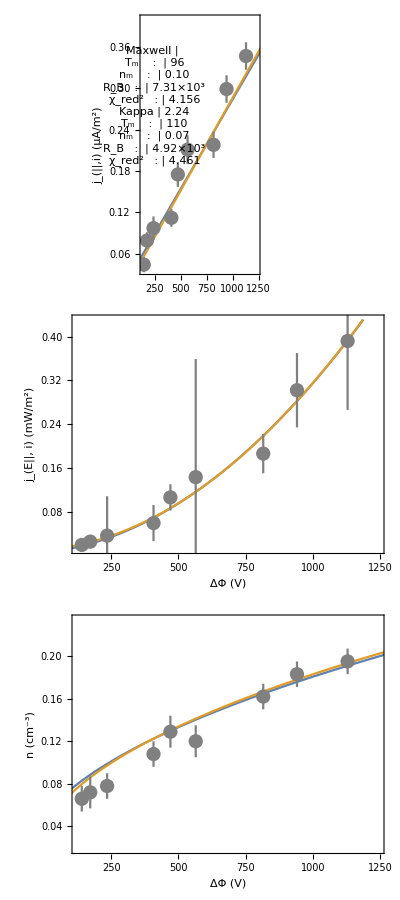

```mathematica
triplePlot=Column[{tripleJVPlot,tripleJeVPlot,tripleDensPlot}]
```

#### Setup plot ranges

```mathematica
minPot=Min[potVal ]* 8/10;maxPot=Max[potVal]*1.1;
```

```mathematica
minJ=Min[curVal]/1.8;maxJ=Max[curVal]*1.2;
minJe=Min[curVal]/1.8;maxJe=Max[curVal]*1.2;
```

#### Other plot stuff

```mathematica
parNames=Style[#,Bold]&/@{"T_m    : ","n_m    : ","R_B   : ","χ_red^2   :"};
pTableVSpace=0.5;
pTableFontSize=14;
pTableScaledLoc={0.12,0.65};
```

```mathematica
titleSize=20;
```

```mathematica
axesLabelSize=18;
```

```mathematica
gJVVals=(MapThread[NumberForm,{({gFitT,gFitN}/.gInitialFitVals),{{3,0},{3,2}}}])~Join~{ScientificForm[gFitRB,3]/.gInitialFitVals}~Join~{NumberForm[gFitChi2red,3]/.gInitialFitVals};
kJVVals=(MapThread[NumberForm,{({kFitT,kFitN}/.kInitialFitVals),{{3,0},{3,2}}}])~Join~{ScientificForm[kFitRB,3]/.kInitialFitVals}~Join~{NumberForm[kFitChi2red,3]/.kInitialFitVals//N};
```

```mathematica
JVParTable=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{Style["Kappa  :",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gJVVals~Join~{(ToString@StringForm["`1`",NumberForm[kFitKappa/.kInitialFitVals,3]])}~Join~kJVVals}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
initTitle=StringJoin@Riffle[tid[[{1,-1}]],"–"];
```

#### Some Monte Carlo stuff for generating current uncertainty and potential uncertainty

```mathematica
inds1
```

{21,22,23,24,25,26,27,28,29}

```mathematica
curErr=curErrs[[inds1]];
jeErr = jeErrs[[inds1]];
densErr=densErrs[[inds1]];
potErr=potErrs[[inds1]];
densPot=densPots[[inds1]];
densPotErr=densPotErrs[[inds1]];
```

```mathematica
genMCCurError:=RandomVariate[NormalDistribution[],nPots]*curErr[[currentInds]]
```

```mathematica
genMCJeError:=RandomVariate[NormalDistribution[],nPots]*jeErr[[currentInds]]
```

```mathematica
genMCNError:=RandomVariate[NormalDistribution[],nPots]*densErr[[currentInds]]
```

```mathematica
genPotVals:=potVal[[currentInds]]+RandomReal[{0,1},nPots]*potErr[[currentInds]]
```

```mathematica
genDensPotVals:=densPot[[currentInds]]+RandomReal[{0,1},nPots]*densPotErr[[currentInds]]
```

```mathematica
inds=Range[1,nPots];
```

#### Visualize, Plot, See what synthetic data look like

```mathematica
currentInds=RandomChoice[inds,nPots];
```

```mathematica
curPotVals=genPotVals;
```

```mathematica
If[donVModel,
curMCNError=genMCNError;
curDensPotVals=genDensPotVals;
curDensErr=densErr[[currentInds]];
curDensWt=1/curDensErr^2;
curDensData=Partition[Riffle[curDensPotVals,((nVKappaIntegrate1D[#,kFitRB/RBFASTtoIonos,kFitT,kFitN,kFitKappa]/.kInitialFitVals)&/@curDensPotVals)+curMCNError],2];
curDensErrData=makeErrorData[curDensPotVals,curDensData[[;;,2]],curDensErr];
]
```

```mathematica
If[doJVModel,
curMCJError=genMCCurError;
curJErr=curErr[[currentInds]];
curJWt=1/curJErr^2;
curJData=Partition[Riffle[curPotVals,((JVKappa[#,kFitRB,kFitT,kFitN,kFitKappa]/.kInitialFitVals)&/@curPotVals)+curMCJError],2];
curJErrData=makeErrorData[curPotVals,curJData[[;;,2]],curJErr];
]
```

```mathematica
If[doJeVModel,
curMCJeError=genMCJeError;
curJeErr=jeErr[[currentInds]];
curJeWt=1/curJeErr^2;
curJeData=Partition[Riffle[curPotVals,((JEVKappa[#,kFitRB,kFitT,kFitN,kFitKappa]/.kInitialFitVals)&/@curPotVals)+curMCJeError],2];
curJeErrData=makeErrorData[curPotVals,curJeData[[;;,2]],curJeErr];
]
```

```mathematica
curTotalData=gFitTotalDataSetup[curDensData,curJData,curJeData,DonVModel->donVModel,DoJVModel->doJVModel,DoJeVModel->doJeVModel];
curTotalWts=gFitTotalWeightSetup[curDensWt,curJWt,curJeWt,DonVModel->donVModel,DoJVModel->doJVModel,DoJeVModel->doJeVModel];
```

```mathematica
JInds=Flatten@Position[curTotalData[[;;,1]],1];
```

```mathematica
JeInds=Flatten@Position[curTotalData[[;;,1]],2];
nInds=Flatten@Position[curTotalData[[;;,1]],3];
```

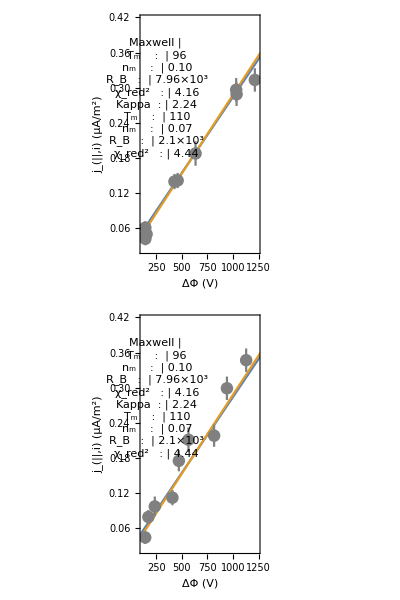

```mathematica
JVInitVsSynthPlot=Column[{Show[Plot[{JVMaxwellian[pot,gFitRB,gFitT,gFitN]/.gInitialFitVals,JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]/.kInitialFitVals},
{pot,minPot*0.8,maxPot*1.3},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",initTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[curJErrData,PlotStyle->Gray]],Show[Plot[{JVMaxwellian[pot,gFitRB,gFitT,gFitN]/.gInitialFitVals,JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]/.kInitialFitVals},
{pot,minPot*0.8,maxPot*1.3},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",initTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jErrData,PlotStyle->Gray]]}]
```

```mathematica
JEVSynthRange=Through[{Min,Max}[curJErrData[[;;,1,2]]]]
```

{0.0416615,0.313211}

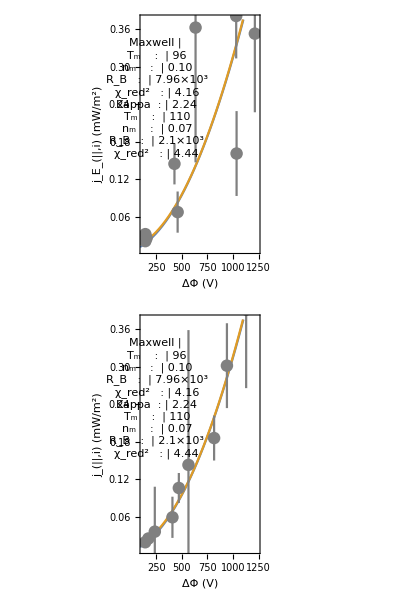

```mathematica
JEVInitVsSynthPlot=Column[{Show[Plot[{JEVMaxwellian[pot,gFitRB,gFitT,gFitN]/.gInitialFitVals,JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]/.kInitialFitVals},
{pot,minPot*0.8,maxPot*1.3},PlotRange->{{minPot,maxPot},{JEVSynthRange[[1]]*0.2,JEVSynthRange[[2]]*1.2}},Frame->True,FrameLabel->{{"j_E_(||,i) (mW/m^2)",""},{"ΔΦ (V)",Style[StringForm["J_E-V Fit (`1`)",initTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[curJeErrData,PlotStyle->Gray]],Show[Plot[{JEVMaxwellian[pot,gFitRB,gFitT,gFitN]/.gInitialFitVals,JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]/.kInitialFitVals},
{pot,minPot*0.8,maxPot*1.3},PlotRange->{{minPot,maxPot},{JEVSynthRange[[1]]*0.2,JEVSynthRange[[2]]*1.2}},Frame->True,FrameLabel->{{"j_(||,i) (mW/m^2)",""},{"ΔΦ (V)",Style[StringForm["J_E-V Fit (`1`)",initTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jeErrData,PlotStyle->Gray]]}]
```

```mathematica
nVSynthRange=Through[{Min,Max}[curDensErrData[[;;,1,2]]]]//N
```

{0.0881969,0.214633}

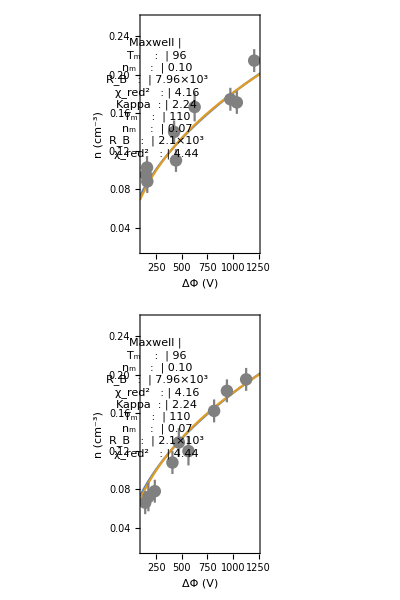

```mathematica
nVInitVsSynthPlot=Column[{Show[Plot[{nVMaxwellian[pot,gFitRB/RBFASTtoIonos,gFitT,gFitN]/.gInitialFitVals,nVKappaIntegrate1D[pot,kFitRB/RBFASTtoIonos,kFitT,kFitN,kFitKappa]/.kInitialFitVals},
{pot,minPot*0.8,maxPot*1.3},PlotRange->{{minPot,maxPot},{nVSynthRange[[1]]*0.2,nVSynthRange[[2]]*1.2}},Frame->True,FrameLabel->{{"n (cm^-3)",""},{"ΔΦ (V)",Style[StringForm["n-V Fit (`1`)",initTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[curDensErrData,PlotStyle->Gray]],Show[Plot[{nVMaxwellian[pot,gFitRB/RBFASTtoIonos,gFitT,gFitN]/.gInitialFitVals,nVKappaIntegrate1D[pot,kFitRB/RBFASTtoIonos,kFitT,kFitN,kFitKappa]/.kInitialFitVals},
{pot,minPot*0.8,maxPot*1.3},PlotRange->{{minPot,maxPot},{nVSynthRange[[1]]*0.2,nVSynthRange[[2]]*1.2}},Frame->True,FrameLabel->{{"n (cm^-3)",""},{"ΔΦ (V)",Style[StringForm["n-V Fit (`1`)",initTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[densErrData,PlotStyle->Gray]]}]
```

```mathematica
If[saveDataFiles,
DumpSave[initFitFile,{kInitialTotalFit,gInitialTotalFit,JVParTable,jErrData,initTitle,tid,jData,jErrData,jWt,potErr,curErr,potVal,curVal}];
Print["Saved "<>initFitFile];]
```

Saved /SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/20180823/itvl2_kappa-fixT110eV_nRolls100_nVJVJeV_initialFits.wdx

Do the Monte Carloing

```mathematica
(*kappamin=1.8;
kappamax=3.3;
Tmin = 40;
Tmax=280;
nmin=0.05;
nmax=2.;
RBmin=8;
RBmax=200;*)
```

```mathematica
kappamin=minFitKappa;
kappamax=maxFitKappa;
Tmin = minFitT;
Tmax=maxFitT;
nmin=minFitN;
nmax=maxFitN;
RBmin=minFitRB;
RBmax=maxFitRB;
```

```mathematica
countItvl=50;
currentInds=inds;
makePlots=True;
```

#### Some options

```mathematica
doBootstrap=False;
log10RBInit=False;
```

#### Kappa block

```mathematica
Block[{trials=nTrials, count=0,currentInds,curPotVals,
curMCNError,curDensPotVals,curDensErr,curDensWt,curDensData,
curMCJError,curJData,curJErr,curJWt,
curMCJeError,curJeData,curJeErr,curJeWt,
curTotalData,curTotalWts,
kinitParams,kFitNinit,kFitTinit,kFitRBinit,kFitKappainit,kTotalFit},
kMCStartupMessage;
kFitVals:=Flatten@Append[{Flatten@Append[{kTotalFit["BestFitParameters"]},kFitValAdds]},kFitChi2red->Total[(kTotalFit["FitResiduals"])^2*curTotalWts]/kDOF]//N;
If[doBootstrap==False,currentInds=inds;];
Monitor[kFits=Table[
(*If[Mod[count,countItvl]==0,Print[ToString@StringForm["Count: `1`",count]]];*)
If[doBootstrap,currentInds=RandomChoice[inds,nPots];];
curPotVals=genPotVals;
If[donVModel,
curMCNError=genMCNError;
curDensPotVals=genDensPotVals;
curDensErr=densErr[[currentInds]];
curDensWt=1/curDensErr^2;
curDensData=Partition[Riffle[curDensPotVals,((nVKappaIntegrate1D[#,kFitRB/RBFASTtoIonos,kFitT,kFitN,kFitKappa]/.kInitialFitVals)&/@curDensPotVals)+curMCNError],2];
];
If[doJVModel,
curMCJError=genMCCurError;
curJErr=curErr[[currentInds]];
curJWt=1/curJErr^2;
curJData=Partition[Riffle[curPotVals,((JVKappa[#,kFitRB,kFitT,kFitN,kFitKappa]/.kInitialFitVals)&/@curPotVals)+curMCJError],2];
];
If[doJeVModel,
curMCJeError=genMCJeError;
curJeErr=jeErr[[currentInds]];
curJeWt=1/curJeErr^2;
curJeData=Partition[Riffle[curPotVals,((JEVKappa[#,kFitRB,kFitT,kFitN,kFitKappa]/.kInitialFitVals)&/@curPotVals)+curMCJeError],2];
];
curTotalData=gFitTotalDataSetup[curDensData,curJData,curJeData,
DonVModel->donVModel,DoJVModel->doJVModel,DoJeVModel->doJeVModel];
curTotalWts=gFitTotalWeightSetup[curDensWt,curJWt,curJeWt,
DonVModel->donVModel,DoJVModel->doJVModel,DoJeVModel->doJeVModel];
kinitParams = RandomReal/@{{nmin,nmax},{Tmin,Tmax},If[log10RBInit,{Log10[RBmin],Log10[RBmax]},{RBmin,RBmax}],{kappamin,kappamax}};
{kFitNinit,kFitTinit,kFitRBinit,kFitKappainit}=kinitParams;
If[log10RBInit,kFitRBinit=10^kFitRBinit];
kTotalFit=NonlinearModelFit[curTotalData,(If[Length@kConstraints≠0,{kTotalModel,kConstraints},kTotalModel]),
kFitVars,
{set,pot},
Weights->totalWts,
VarianceEstimatorFunction->(1&),
Method->fitMethod];
count++;
(*{count, kFit["BestFitParameters"],kinitParams,kFit},trials];]*)
{count,Evaluate[ kFitOutput/.kFitVals],kinitParams,kTotalFit},trials];,count]
];
```

Interval: 2

fixT    : 110

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

```mathematica
kDataFileTmp = kDataFile;
```

```mathematica
count=0;
```

```mathematica
While[FileExistsQ[saveDir<>kDataFileTmp],
count =count+1;
kDataFileTmp=orbPref<>kFString<>"-"<>IntegerString[count,10,2]<>datFSuff;
]
```

```mathematica
If[saveDataFiles,DumpSave[(saveDir<>kDataFileTmp),kFits];Print["Saved to "<>saveDir<>kDataFileTmp]]
```

Saved to /SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/20180815/Orb4682_itvl2_kappa-fixT110eV_nRolls600_nVJVJeV.wdx

#### Maxwell block

```mathematica
Block[{trials=nTrials, count=0,currentInds,curPotVals,
curMCNError,curDensPotVals,curDensErr,curDensWt,curDensData,
curMCJError,curJData,curJErr,curJWt,
curMCJeError,curJeData,curJeErr,curJeWt,
curTotalData,curTotalWts,
ginitParams,gFitNinit,gFitTinit,gFitRBinit,gFitKappainit,gTotalFit},
gMCStartupMessage;
gFitVals:=Flatten@Append[{Flatten@Append[{gTotalFit["BestFitParameters"]},gFitValAdds]},gFitChi2red->Total[(gTotalFit["FitResiduals"])^2*curTotalWts]/gDOF];
If[doBootstrap==False,currentInds=inds;];
Monitor[gFits=Table[
(*If[Mod[count,countItvl]==0,Print[ToString@StringForm["Count: `1`",count]]];*)
If[doBootstrap,currentInds=RandomChoice[inds,nPots];];
curPotVals=genPotVals;
If[donVModel,
curMCNError=genMCNError;
curDensPotVals=genDensPotVals;
curDensErr=densErr[[currentInds]];
curDensWt=1/curDensErr^2;
curDensData=Partition[Riffle[curDensPotVals,((nVMaxwellian[#,gFitRB/RBFASTtoIonos,gFitT,gFitN]/.gInitialFitVals)&/@curDensPotVals)+curMCNError],2];
];
If[doJVModel,
curMCJError=genMCCurError;
curJErr=curErr[[currentInds]];
curJWt=1/curJErr^2;
curJData=Partition[Riffle[curPotVals,((JVMaxwellian[#,gFitRB,gFitT,gFitN]/.gInitialFitVals)&/@curPotVals)+curMCJError],2];
];
If[doJeVModel,
curMCJeError=genMCJeError;
curJeErr=jeErr[[currentInds]];
curJeWt=1/curJeErr^2;
curJeData=Partition[Riffle[curPotVals,((JEVMaxwellian[#,gFitRB,gFitT,gFitN]/.gInitialFitVals)&/@curPotVals)+curMCJeError],2];
];
curTotalData=gFitTotalDataSetup[curDensData,curJData,curJeData,
DonVModel->donVModel,DoJVModel->doJVModel,DoJeVModel->doJeVModel];
curTotalWts=gFitTotalWeightSetup[curDensWt,curJWt,curJeWt,
DonVModel->donVModel,DoJVModel->doJVModel,DoJeVModel->doJeVModel];
ginitParams = RandomReal/@{{nmin,nmax},{Tmin,Tmax},If[log10RBInit,{Log10[RBmin],Log10[RBmax]},{RBmin,RBmax}]};
{gFitNinit,gFitTinit,gFitRBinit}=ginitParams;
If[log10RBInit,gFitRBinit=10^gFitRBinit];
gTotalFit=NonlinearModelFit[curTotalData,(If[Length@gConstraints≠0,{gTotalModel,gConstraints},gTotalModel]),
gFitVars,
{set,pot},
Weights->totalWts,
VarianceEstimatorFunction->(1&),
Method->fitMethod];
count++;
(*{count, kFit["BestFitParameters"],kinitParams,kFit},trials];]*)
{count,Evaluate[ gFitOutput/.gFitVals],ginitParams,gTotalFit},trials];,count]
];
```

Interval: 2

fixT    : 96

```mathematica
gDataFileTmp = gDataFile;
```

```mathematica
count=0;
```

```mathematica
While[FileExistsQ[saveDir<>gDataFileTmp],
count =count+1;
gDataFileTmp=orbPref<>gFString<>"-"<>IntegerString[count,10,2]<>datFSuff;
]
```

```mathematica
If[saveDataFiles,DumpSave [saveDir<>gDataFileTmp,gFits];Print["Saved to "<>saveDir<>gDataFileTmp]]
```

Saved to /SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/20180815/Orb4682_itvl2_Maxwell-fixT96eV_nRolls1000_nVJVJeV.wdx

Now check ‘em out

```mathematica
ListLogLinearPlot[Partition[Riffle[kMCVals[[4,;;]],kMCVals[[1,;;]]],2],Frame->True,FrameLabel->{"Kappa","Dens"}]
```

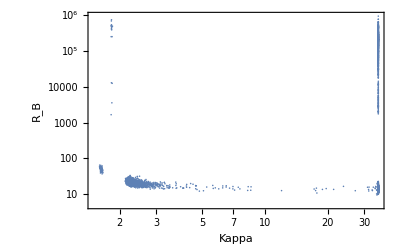

```mathematica
ListLogLogPlot[Partition[Riffle[kMCVals[[4,;;]],kMCVals[[3,;;]]],2],Frame->True,FrameLabel->{"Kappa","R_B"}]
```

#### RESTORE DATA FILES

```mathematica
If[FileExistsQ[saveDir<>kDataFile],<<(saveDir<>kDataFile);
Print["Restored "<>saveDir<>kDataFile];
]
```

Restored /SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/20180609/Orb1607_itvl1_kappa-fixT75eV_nRolls5000_JVJeV.wdx

```mathematica
If[FileExistsQ[saveDir<>gDataFile],<<(saveDir<>gDataFile);
Print["Restored "<>saveDir<>gDataFile];
]
```

Restored /SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/20180609/Orb1607_itvl1_Maxwell-fixT70eV_nRolls5000_JVJeV.wdx

```mathematica
kMCVals=((kFits[[;;,2]])[[;;,#]])&/@{1,2,3,4};
```

```mathematica
gMCVals=((gFits[[;;,2]])[[;;,#]])&/@{1,2,3};
```

```mathematica
kMCTitles={"N (cm^-3)","T (eV)","R_B","κ"};
kMCPDFTitles={"PDF (cm^3)","PDF (eV^-1)","PDF (R_B^-1)","PDF (κ^-1)"};
gMCTitles={"N (cm^-3)","T (eV)","R_B"};
```

```mathematica
binSizes=Table[Automatic,4];
```

```mathematica
binSizes={{0.005},{0.2},{100},{0.2}};
```

```mathematica
MCTitle=StringJoin@Riffle[tid[[{1,-1}]],"–"];
```

```mathematica
densPlotRange:=Switch[interval,1,{{0,6},{0.3,1.3}},2,{{0,80},{0.4,1.2}}];
```

## Kappa plots

#### fixT=75 eV, nRoll= 5000

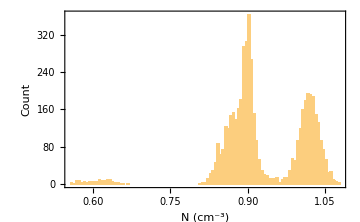
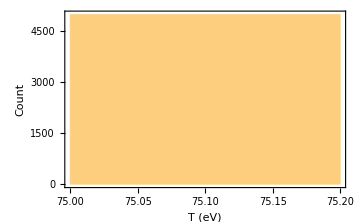
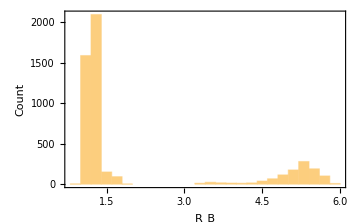
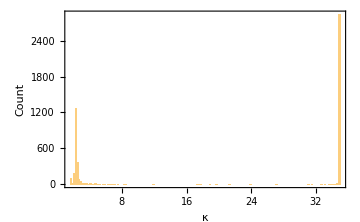

```mathematica
kHistosPlot=Row[Table[Histogram[If[MCParmInd==3,Log10[kMCVals[[MCParmInd]]],kMCVals[[MCParmInd]]],If[MCParmInd==3,Automatic,binSizes[[MCParmInd]]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],"Count"},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

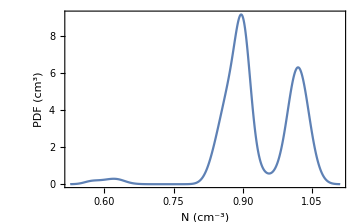
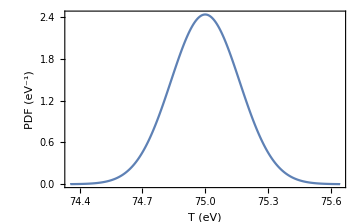
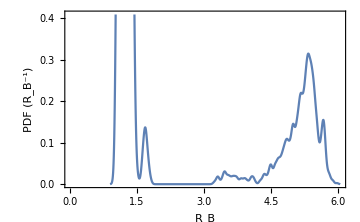
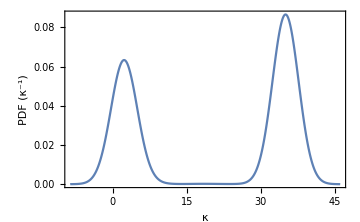

```mathematica
kSmoothHistosPlot=Row[Table[SmoothHistogram[If[MCParmInd≠ 3,kMCVals[[MCParmInd]],Log10[kMCVals[[MCParmInd]]]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],kMCPDFTitles[[MCParmInd]]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

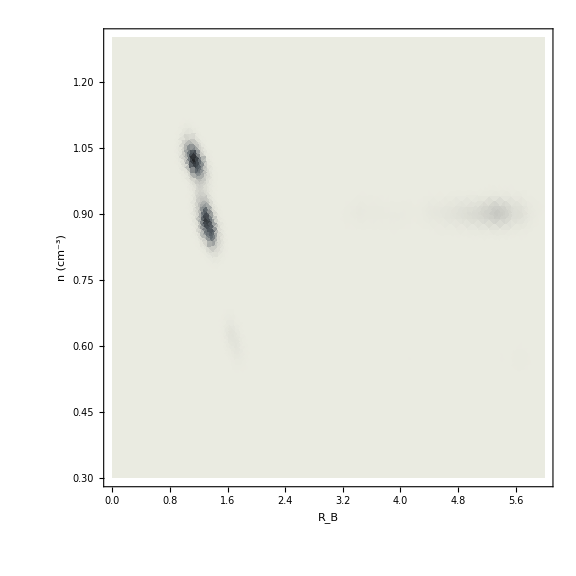

```mathematica
kDensityHisto=SmoothDensityHistogram[Partition[Riffle[Log10[kMCVals[[3]]],kMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Kappa, N = `2`)",MCTitle,nTrials],Bold,20]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]]
```

```mathematica
If[makePlots,Print["Making plots in "<>dir<>" ..."];
Print[kDensityHistoFile<>" ..."];
Export[plotDir<>kDensityHistoFile,kDensityHisto];
Print[kHistosPlotFile<>" ..."];
Export[plotDir<>kHistosPlotFile,kHistosPlot];
Print[kSmoothHistosPlotFile<>" ..."];
Export[plotDir<>kSmoothHistosPlotFile,kSmoothHistosPlot];
Print["Done!"]]
```

Making plots in /SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/ ...

Orb1607_itvl1_kappa-fixT75eV_nRolls5000_JVJeV__smoothDensityHistogram.pdf ...

Orb1607_itvl1_kappa-fixT75eV_nRolls5000_JVJeV__histograms.pdf ...

Orb1607_itvl1_Maxwell-fixT70eV_nRolls5000_JVJeV__smoothHistograms.pdf ...

Done!

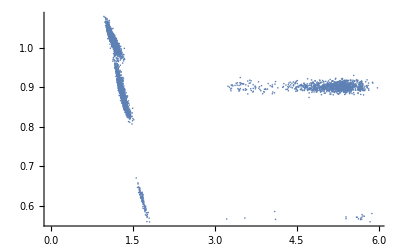

```mathematica
ListPlot[Partition[Riffle[Log10[kMCVals[[3]]],kMCVals[[1]]],2]]
```

## Maxwellian plots

#### Itvl 1, fixT=133 eV, nRoll= 5000

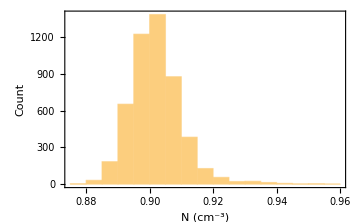
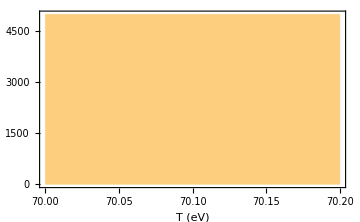
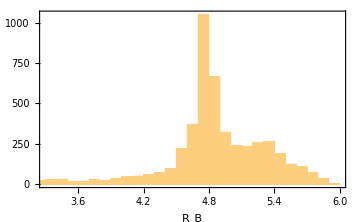

```mathematica
Row[Table[Histogram[If[MCParmInd≠ 3,gMCVals[[MCParmInd]],Log10[gMCVals[[MCParmInd]]]],If[MCParmInd≠ 3,binSizes[[MCParmInd]],Automatic],ImageSize->Medium,Frame->True,FrameLabel->{gMCTitles[[MCParmInd]],If[MCParmInd==1,"Count",""]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3}}]]
```

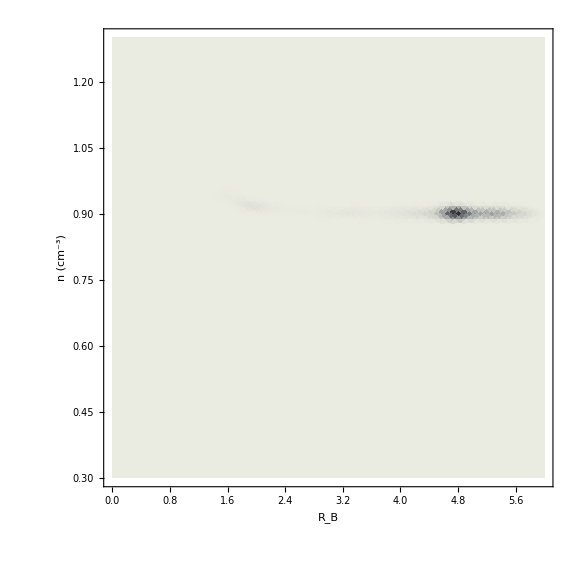

```mathematica
SmoothDensityHistogram[Partition[Riffle[Log10[gMCVals[[3]]],gMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Maxwellian, N = `2`)",MCTitle,nTrials],Bold,20]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]]
```

## 20180609 keeper plots

#### Initial fits

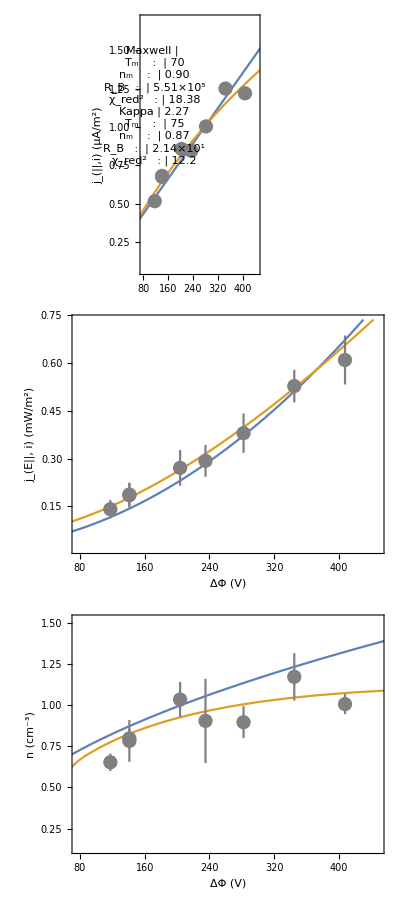

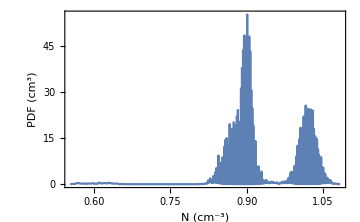
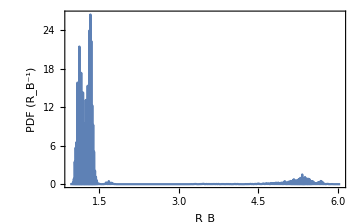
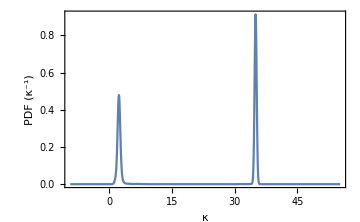
-Graphics--Graphics--Graphics--Graphics-

```mathematica
kSmoothHistosPlot=Row[Table[SmoothHistogram[If[MCParmInd≠ 3,kMCVals[[MCParmInd]],Log10[kMCVals[[MCParmInd]]]],If[MCParmInd≠2,{"Adaptive",Automatic,1.},Automatic],ImageSize->Medium,PlotRange->Full,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],kMCPDFTitles[[MCParmInd]]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

```mathematica
highKappa=Flatten@Position[kMCVals[[4,;;]],x_/;x≥ 5];
```

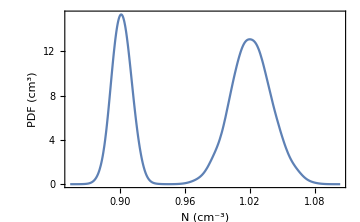
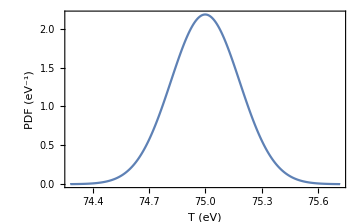
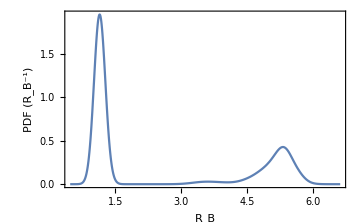
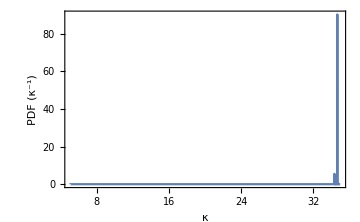

```mathematica
kSmoothHistosPlot=Row[Table[SmoothHistogram[If[MCParmInd≠ 3,kMCVals[[MCParmInd,highKappa]],Log10[kMCVals[[MCParmInd,highKappa]]]],If[MCParmInd≠2,{"Adaptive",Automatic,Switch[MCParmInd,1,0.2,3,0.4,4,0.2]},Automatic],ImageSize->Medium,PlotRange->Full,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],kMCPDFTitles[[MCParmInd]]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

Eliminate high-kappa cases

```mathematica
goodKappa=Flatten@Position[kMCVals[[4,;;]],x_/;x<5&&x>2.0];
```

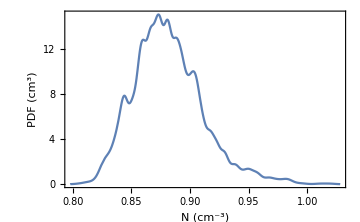
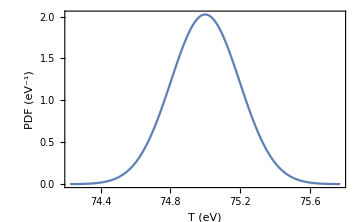
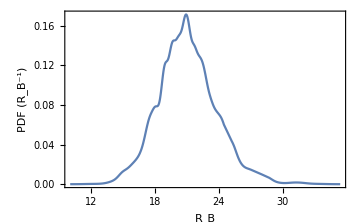
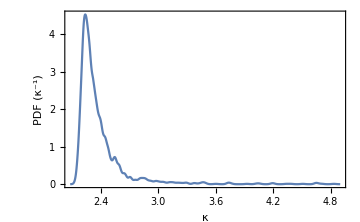

```mathematica
kSmoothHistosPlot=Row[Table[SmoothHistogram[If[MCParmInd≠ 3,kMCVals[[MCParmInd,goodKappa]],kMCVals[[MCParmInd,goodKappa]]],If[MCParmInd≠2,{"Adaptive",Automatic,Switch[MCParmInd,1,0.2,3,0.4,4,0.2]},Automatic],ImageSize->Medium,PlotRange->Full,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],kMCPDFTitles[[MCParmInd]]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

```mathematica
lowKappa=Flatten@Position[kMCVals[[4,;;]],x_/;x≤ 2.0];
```

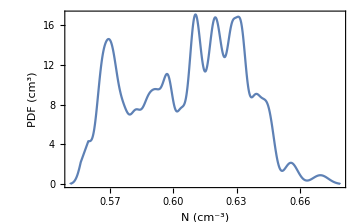
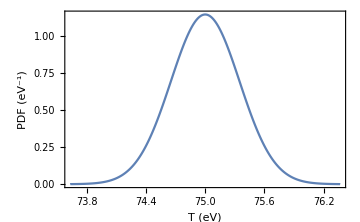
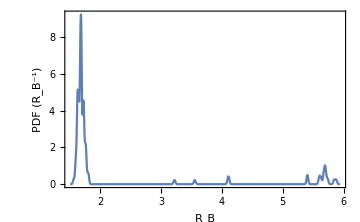
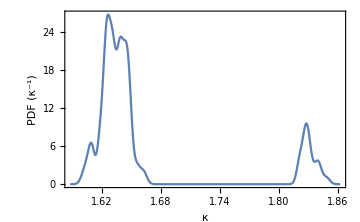

```mathematica
kSmoothHistosPlot=Row[Table[SmoothHistogram[If[MCParmInd≠ 3,kMCVals[[MCParmInd,lowKappa]],Log10[kMCVals[[MCParmInd,lowKappa]]]],If[MCParmInd≠2,{"Adaptive",Automatic,Switch[MCParmInd,1,0.4,3,0.3,4,0.2]},Automatic],ImageSize->Medium,PlotRange->Full,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],kMCPDFTitles[[MCParmInd]]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

#### Kappa plots

```mathematica
kHistosPlot=Row[Table[Histogram[If[MCParmInd==3,Log10[kMCVals[[MCParmInd]]],kMCVals[[MCParmInd]]],If[MCParmInd==3,Automatic,binSizes[[MCParmInd]]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],"Count"},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

-Graphics--Graphics--Graphics--Graphics-

```mathematica
kSmoothHistosPlot=Row[Table[SmoothHistogram[If[MCParmInd≠ 3,kMCVals[[MCParmInd]],Log10[kMCVals[[MCParmInd]]]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],kMCPDFTitles[[MCParmInd]]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

-Graphics--Graphics--Graphics--Graphics-

```mathematica
kHistoRBKappa=Table[SmoothDensityHistogram[Partition[Riffle[Log10[kMCVals[[3]]],kMCVals[[4]]],2],bw,ImageSize->Large,Frame->True,FrameStyle->FontSize->16, PlotRange->{{Min[Log10[kMCVals[[3]]]],Max[Log10[kMCVals[[3]]]]},Automatic},FrameLabel->{{"κ",""},{"R_B",Style[ToString@StringForm["`1` (Kappa, N = `2`)",MCTitle,nTrials],Bold,20]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]],{bw,{{"Adaptive",Automatic,0.25},{"Adaptive",Automatic,0.75}}}]
```

$Aborted

```mathematica
kDensityHisto=SmoothDensityHistogram[Partition[Riffle[Log10[kMCVals[[3]]],kMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Kappa, N = `2`)",MCTitle,nTrials],Bold,20]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]]
```

-Graphics-

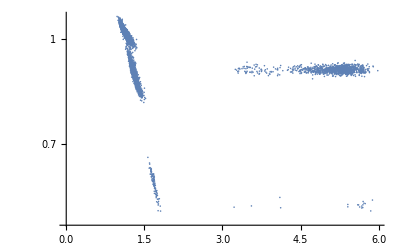

```mathematica
ListLogPlot[Partition[Riffle[Log10[kMCVals[[3]]],kMCVals[[1]]],2]]
```

#### Maxwellian plots

```mathematica
SmoothDensityHistogram[Partition[Riffle[Log10[gMCVals[[3]]],gMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Maxwellian, N = `2`)",MCTitle,nTrials],Bold,20]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]]
```

-Graphics-

```mathematica
Row[Table[Histogram[If[MCParmInd≠ 3,gMCVals[[MCParmInd]],Log10[gMCVals[[MCParmInd]]]],If[MCParmInd≠ 3,binSizes[[MCParmInd]],Automatic],ImageSize->Medium,Frame->True,FrameLabel->{gMCTitles[[MCParmInd]],If[MCParmInd==1,"Count",""]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3}}]]
```

-Graphics--Graphics--Graphics-